```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FCClearScalarProducts[];
SP[p,p]=s;
```

```mathematica
Const1[x_]:=1;
Const0[x_]:=0;
evalLoop[ex_]:=ex//TID[#,q,ToPaVe->True]&//DotSimplify[#,Expanding->False]&//DiracSimplify[#,DiracSubstitute67->True]&//Collect2[#,{A0,B0,C0,D0}]&;
processLoop[exs_]:=(
a1=FCTraceFactor/@DotSimplify[#,Expanding->False]&/@exs;
a2=evalLoop/@a1;
a3=Total[a2];
a4=ChangeDimension[PaXEvaluate[a3],4]//Expand
)
```

```mathematica
LoopAmp[0]={(ⅈ el^2)/(16 π^4) FeynAmpDenominator[PropagatorDenominator[Momentum[q,D],m],PropagatorDenominator[Momentum[-p+q,D],0]] (Pair[Momentum[p,D],Momentum[p,D]]+2 Pair[Momentum[p,D],Momentum[q,D]]+Pair[Momentum[q,D],Momentum[q,D]])}
AmpCT[0]=s FR$deltaZ-M(2 FR$deltaM+M FR$deltaZ);
```

{(ⅈ el^2 (2 (p·q)+p^2+q^2))/(16 π^4 (q^2-m^2).(q-p)^2)}

```mathematica
LoopAmp[1]=LoopAmp[0]//processLoop;
LoopAmp[2]=(LoopAmp[1]+AmpCT[0])//Expand;
Repart=(Re[LoopAmp[2]] // ComplexExpand);
Impart=(Im[LoopAmp[2]] // ComplexExpand);
```

Get::noopen: Cannot open C:\Users\HEP-ph\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
RNCond1=Simplify[Repart/.{s->M^2},Assumptions->M>0]//Refine[#,Assumptions->{M>m>0}]&;
RNCond2=Simplify[D[Repart,s]/.{s->M^2},Assumptions->M>0]//Refine[#,Assumptions->{M>m>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$deltaM,FR$deltaZ}];
```

```mathematica
AmpReLeft=(Repart/.RNRes[[1]])/.ScaleMu->1//Refine[#,Assumptions->{M>m>0,Im[s]>0}]&//FullSimplify[#,Assumptions->{m>0}]&;
```

```mathematica
ReLeft[s1_,m1_,coup_]:=AmpReLeft/.{s->s1,M->1,m->m1,el->4π √coup};
```

```mathematica
RNCond1=Simplify[Repart/.{s->M^2},Assumptions->M>0]//Refine[#,Assumptions->{m>M>0}]&;
RNCond2=Simplify[D[Repart,s]/.{s->M^2},Assumptions->M>0]//Refine[#,Assumptions->{m>M>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$deltaM,FR$deltaZ}];
```

```mathematica
AmpReRight=(Repart/.RNRes[[1]])/.ScaleMu->1//Refine[#,Assumptions->{m>M>0,Im[s]>0}]&//FullSimplify[#,Assumptions->{m>0}]&;
```

```mathematica
ReRight[s1_,m1_,coup_]:=AmpReRight/.{s->s1,M->1,m->m1,el->4π √coup};
AmpIm[s1_,m1_,coup_]:=Impart/.{s->s1,M->1,m->m1,el->4π √coup};
```

```mathematica
Amp[s_,m_,coup_]:=If[m>1,ReRight[s,m,coup],ReLeft[s,m,coup]]+ⅈ AmpIm[s,m,coup];
```

```mathematica
TotalAmp1[s_]:=Amp[s,0.9,0.03];
TotalAmp2[s_]:=Amp[s,1.1,0.03];
```

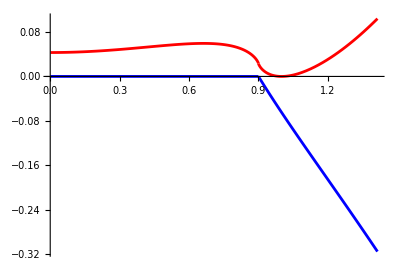

```mathematica
Show[ParametricPlot[{Sqrt[s],Re[TotalAmp1[s]]},{s,-0,2},MaxRecursion->10,PlotStyle->{Red}],ParametricPlot[{Sqrt[s],Im[TotalAmp1[s]]},{s,-0,2},MaxRecursion->10,PlotStyle->{Blue}],PlotRange->Full,AspectRatio->0.7]
```

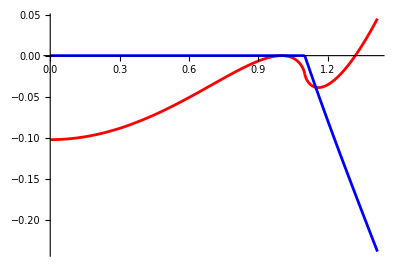

```mathematica
Show[ParametricPlot[{Sqrt[s],Re[TotalAmp2[s]]},{s,-0,2},MaxRecursion->10,PlotStyle->{Red}],ParametricPlot[{Sqrt[s],Im[TotalAmp2[s]]},{s,-0,2},MaxRecursion->10,PlotStyle->{Blue}],PlotRange->Full,AspectRatio->0.7]
```

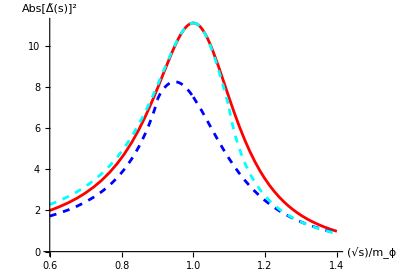

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+0.3ⅈ]^-2},{s,0.36,1.96},MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Abs[OverTilde[Δ][s]]^2},PlotStyle->{Red}],ParametricPlot[{Sqrt[s],Abs[s-1+0.3ⅈ-TotalAmp1[s]]^-2},{s,0.36,1.96},MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Abs[OverTilde[Δ][s]]^2},PlotStyle->{Dashed, Blue}],ParametricPlot[{Sqrt[s],Abs[s-1+0.3ⅈ-TotalAmp2[s]]^-2},{s,0.36,1.96},MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Abs[OverTilde[Δ][s]]^2},PlotStyle->{Dashed, Cyan}],AspectRatio->0.7]
```